This notebook explores the composition as a function of space of the primary dressed eigenstate in the bubble condensate.

Requires bubble-4a-murphree.nb to be run.

First examine the energies and eigenstates of the trap without dressing. The highest energy state is |2,2>, then next highest |2,1>, and so on; this allows us to label our states.

Problem assigning eigenvector and eigenvalue consistently. Could be done by hand for a discrete plot, e.g. ListPlot, by making sure that the eigenvalue and eigenvector components change smoothly over the range.

```mathematica
AdiabaticEnergiesChipC2All@@({0,(*Ωc*)0}~Join~(z0[CurrL, CurrZ,CurrH,Bx1,By1,Bz1]⟦All,2⟧))
AdiabaticVectorsChipC@@({0,(*Ωc*)0}~Join~(z0[CurrL, CurrZ,CurrH,Bx1,By1,Bz1]⟦All,2⟧))
```

{-6.97052×10^6,6.97052×10^6,3.49061×10^6,-3.4799×10^6,7137.38}

{{1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.},{0.,0.,0.,1.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.}}

```mathematica
stateLabels={"-2","-1","0","1","2"};
stateColors={Red,Orange,Yellow,Green,Blue};
ourState=1;
```

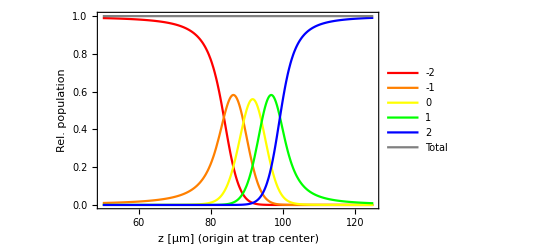

```mathematica
offsetTemp=50;
widthTemp=75;
minTemp=z0[CurrL, CurrZ,CurrH,Bx1,By1,Bz1]⟦All,2⟧;
Show[MapThread[Plot[(AdiabaticVectorsChipC@@({Δ1,Ωc}~Join~(minTemp⟦1;;2⟧)~Join~{(z*10^(-6)+minTemp⟦3⟧)}))⟦ourState,#1⟧^2,{z,offsetTemp,offsetTemp+widthTemp},PlotStyle->#2,PlotRange->All,PlotLegends->{#3},FrameLabel->{"z [μm] (origin at trap center)","Rel. population"},Frame->True]&,{Range[5],stateColors,stateLabels}]
~Join~
{Plot[Total[#^2&/@(AdiabaticVectorsChipC@@({Δ1,Ωc}~Join~(minTemp⟦1;;2⟧)~Join~{(z*10^(-6)+minTemp⟦3⟧)}))⟦ourState⟧],{z,offsetTemp,offsetTemp+widthTemp},PlotStyle->Gray,PlotLegends->{"Total"}]}
]
```

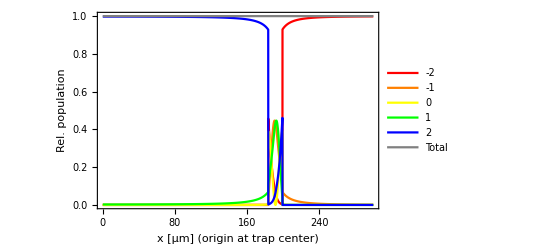

```mathematica
offsetTemp=0;
widthTemp=300;
minTemp=z0[CurrL, CurrZ,CurrH,Bx1,By1,Bz1]⟦All,2⟧;
Show[MapThread[Plot[(AdiabaticVectorsChipC@@({Δ1,Ωc}~Join~{x*10^(-6)+minTemp⟦1⟧}~Join~(minTemp⟦2;;3⟧)))⟦ourState,#1⟧^2,{x,offsetTemp,offsetTemp+widthTemp},PlotStyle->#2,PlotRange->All,PlotLegends->{#3},FrameLabel->{"x [μm] (origin at trap center)","Rel. population"},Frame->True]&,{Range[5],stateColors,stateLabels}]
~Join~
{Plot[Total[#^2&/@(AdiabaticVectorsChipC@@({Δ1,Ωc}~Join~{x*10^(-6)+minTemp⟦1⟧}~Join~(minTemp⟦2;;3⟧)))⟦ourState⟧],{x,offsetTemp,offsetTemp+widthTemp},PlotStyle->Gray,PlotLegends->{"Total"}]}
]
```